Functions to be used in the calculations

```mathematica
CayleyMenger[d12_,d13_,d14_,d23_,d24_,d34_]:=
{{0,d12^2,d13^2,d14^2,1},
{d12^2,0,d23^2,d24^2,1},
{d13^2,d23^2,0,d34^2,1},
{d14^2,d24^2,d34^2,0,1},
{1,1,1,1,0}}//Det;
Vol[d12_,d13_,d14_,d23_,d24_,d34_]:= Sqrt[CayleyMenger[d12,d13,d14,d23,d24,d34]/288];

Heron[x_, y_, z_]:= 1/4 Sqrt[(x+y+z)(x+y-z)(y+z-x)(z+x-y)];SurfArea[d12_,d13_,d14_,d23_,d24_,d34_] := Heron[d12,d13,d23]+Heron[d12,d14,d24]+Heron[d13,d14,d34]+Heron[d23,d24,d34];

NormalizedSurfArea[d12_,d13_,d14_,d23_,d24_,d34_]:= SurfArea[d12,d13,d14,d23,d24,d34]/Vol[d12,d13,d14,d23,d24,d34]^(2/3);
```

Calculation of Isoperimetric Tile from First Goldberg Family

```mathematica
surfarea=NormalizedSurfArea[1,Sqrt[3 a^2+1],3 a,1,Sqrt[3 a^2+1],1]//FullSimplify[#,a>0]&
```

((2/3)^(1/3) √(1-a^2) (6 a+√(3+9 a^2)))/((a^2 (-1+a^2)^2)^(1/3))

```mathematica
Minimize[{surfarea,a>0},a]
```

{2 2^(5/6) 3^(2/3),{a→1/3}}

```mathematica
Minimize[{surfarea,a>0},a]//N
```

{7.41258,{a→0.333333}}

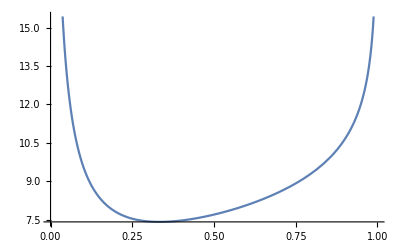

```mathematica
Plot[surfarea,{a,0,1}]
```

Calculation for Isoperimetric Tile of Second Goldberg Family:

```mathematica
surfarea=NormalizedSurfArea[1,Sqrt[3 a^2+1],3 a/2,1,Sqrt[4-3a^2]/2,Sqrt[4-3a^2]/2]//FullSimplify[#,a>0]&
```

(√(1-a^2) (√3+6 a+√(3+9 a^2)))/(3^(1/3) (a^2 (-1+a^2)^2)^(1/3))

```mathematica
Minimize[{surfarea,a>0},a]
```

{(√3+6 Root[{-3+#1^2&,8 #1-36 #2+12 #1 #2^2+27 #2^3-84 #1 #2^4+189 #2^5-8 #1 #2^6-450 #2^7+288 #1 #2^8+486 #2^9-324 #1 #2^10-297 #2^11+108 #1 #2^12+81 #2^13&},{2,6}]+√(3 (1+3 Root[{-3+#1^2&,8 #1-36 #2+12 #1 #2^2+27 #2^3-84 #1 #2^4+189 #2^5-8 #1 #2^6-450 #2^7+288 #1 #2^8+486 #2^9-324 #1 #2^10-297 #2^11+108 #1 #2^12+81 #2^13&},{2,6}]^2)))/(3^(1/3) Root[{-3+#1^2&,8 #1-36 #2+12 #1 #2^2+27 #2^3-84 #1 #2^4+189 #2^5-8 #1 #2^6-450 #2^7+288 #1 #2^8+486 #2^9-324 #1 #2^10-297 #2^11+108 #1 #2^12+81 #2^13&},{2,6}]^(2/3) (1-Root[{-3+#1^2&,8 #1-36 #2+12 #1 #2^2+27 #2^3-84 #1 #2^4+189 #2^5-8 #1 #2^6-450 #2^7+288 #1 #2^8+486 #2^9-324 #1 #2^10-297 #2^11+108 #1 #2^12+81 #2^13&},{2,6}]^2)^(1/6)),{a→Root[{-3+#1^2&,8 #1-36 #2+12 #1 #2^2+27 #2^3-84 #1 #2^4+189 #2^5-8 #1 #2^6-450 #2^7+288 #1 #2^8+486 #2^9-324 #1 #2^10-297 #2^11+108 #1 #2^12+81 #2^13&},{2,6}]}}

```mathematica
Minimize[{surfarea,a>0},a]//N
```

{8.109,{a→0.490781}}

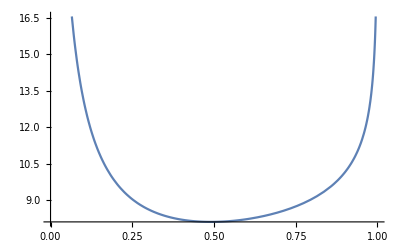

```mathematica
Plot[surfarea,{a,0,1}]
```

Calculation for Isoperimetric Tile from Third Goldberg Family:

```mathematica
surfarea=NormalizedSurfArea[1,Sqrt[6a^2+3]/2,3a,1/2,Sqrt[3a^2+1],Sqrt[6a^2+3]/2]//FullSimplify[#,a>0]&
```

(√(1-a^2) (3 (2+√3) a+√(3+9 a^2)))/(3^(1/3) (a^2 (-1+a^2)^2)^(1/3))

```mathematica
Minimize[{surfarea,a>0},a]
```

{(6 Root[{-3+#1^2&,12-16 #1+9 #2^2+144 #1 #2^2+279 #2^4+96 #1 #2^4+42 #2^6-992 #1 #2^6-2070 #2^8+1200 #1 #2^8+2781 #2^10-432 #1 #2^10-1053 #2^12&},{2,5}]+3 √3 Root[{-3+#1^2&,12-16 #1+9 #2^2+144 #1 #2^2+279 #2^4+96 #1 #2^4+42 #2^6-992 #1 #2^6-2070 #2^8+1200 #1 #2^8+2781 #2^10-432 #1 #2^10-1053 #2^12&},{2,5}]+√(3 (1+3 Root[{-3+#1^2&,12-16 #1+9 #2^2+144 #1 #2^2+279 #2^4+96 #1 #2^4+42 #2^6-992 #1 #2^6-2070 #2^8+1200 #1 #2^8+2781 #2^10-432 #1 #2^10-1053 #2^12&},{2,5}]^2)))/(3^(1/3) Root[{-3+#1^2&,12-16 #1+9 #2^2+144 #1 #2^2+279 #2^4+96 #1 #2^4+42 #2^6-992 #1 #2^6-2070 #2^8+1200 #1 #2^8+2781 #2^10-432 #1 #2^10-1053 #2^12&},{2,5}]^(2/3) (1-Root[{-3+#1^2&,12-16 #1+9 #2^2+144 #1 #2^2+279 #2^4+96 #1 #2^4+42 #2^6-992 #1 #2^6-2070 #2^8+1200 #1 #2^8+2781 #2^10-432 #1 #2^10-1053 #2^12&},{2,5}]^2)^(1/6)),{a→Root[{-3+#1^2&,12-16 #1+9 #2^2+144 #1 #2^2+279 #2^4+96 #1 #2^4+42 #2^6-992 #1 #2^6-2070 #2^8+1200 #1 #2^8+2781 #2^10-432 #1 #2^10-1053 #2^12&},{2,5}]}}

```mathematica
Minimize[{surfarea,a>0},a]//N
```

{8.27318,{a→0.23764}}

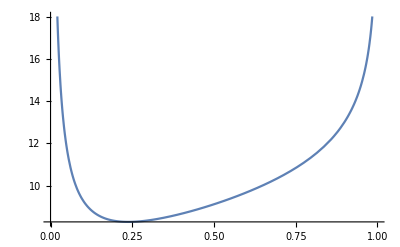

```mathematica
Plot[surfarea,{a,0,1}]
```